```mathematica
f[x_]:=Sin[x]/x
f[{-1,-.5,-.1,-.05,-.01,.01,.05,.1,.5,1}]//N
Limit[f[x],x->0]
```

{0.841471,0.958851,0.998334,0.999583,0.999983,0.999983,0.999583,0.998334,0.958851,0.841471}

1

```mathematica
{-1,0.958851077208406,0.9983341664682815,0.9995833854135666,0.9999833334166665,0.9999833334166665,0.9995833854135666,0.9983341664682815,0.958851077208406}
```

1

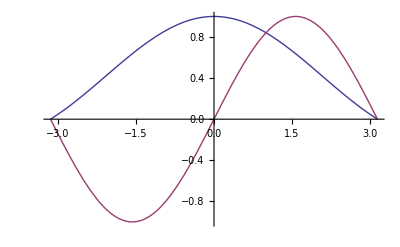

```mathematica
Plot[{f[x],Sin[x]}, {x,-Pi,Pi}]
```

```mathematica
Export["example1.pdf",%32,"PDF"]
```

example1.pdf

{-0.459698,-0.244835,-0.0499583,-0.0249948,-0.00499996,0.00499996,0.0249948,0.0499583,0.244835,0.459698}

0

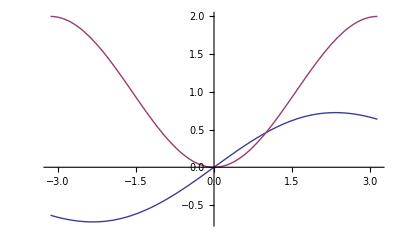

```mathematica
f[x_]:=(1-Cos[x])/x
f[{-1,-.5,-.1,-.05,-.01,.01,.05,.1,.5,1}]//N
Limit[f[x],x->0]
Plot[{f[x],1-Cos[x]}, {x,-Pi,Pi}]
```

```mathematica
Export["example2.pdf",%45,"PDF"]
```

example2.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["example2.pdf"]]]
```

```mathematica
Directory[]
```

/Users/edwint

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/edwint/Documents/U/ubb/sccc/calculus/week02/notes

```mathematica
NotebookDirectory[]
```

/Users/edwint/Documents/U/ubb/sccc/calculus/week02/notes/